```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

```mathematica
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = { -F[9],F[9]} -> {V[4],V[4]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],V[4],F[9]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 3 Particles insertions

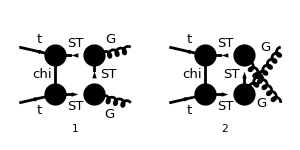

```mathematica
goodDiags=DiagramExtract[allDiags,{2,3}];
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p1,p2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{-p3,-p4},LoopMomenta->{q},SUNIndexNames->{c3,c4,c3,c4},SUNFIndexNames->{c1,c2},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[FCReplaceMomenta[SUNSimplify[DiracSimplify[ampA]],{p4-> -p1-p2-p3}]]]
```

in total: 2 Particles amplitudes

gs^2 yDM^2 (γ·q).(γ̄)^6 (((2 p1^μ+p3^μ-2 q^μ) (T^c3 T^c4)_c1c2 (p1^ν-p2^ν+p3^ν-2 q^ν))/((q^2-mChi^2).((p2+q)^2-mST^2).((-p1-p3+q)^2-mST^2).((q-p1)^2-mST^2))-((2 p2^μ+p3^μ+2 q^μ) (T^c4 T^c3)_c1c2 (p1^ν-p2^ν-p3^ν-2 q^ν))/((q^2-mChi^2).((p2+q)^2-mST^2).((p2+p3+q)^2-mST^2).((q-p1)^2-mST^2)))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,p3,p4,MT,MT,0,0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]]/.{s+t+u-> 2 MT^2};
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(D_0(MT^2,MT^2,0,0,s,t,mST^2,mChi^2,mST^2,mST^2) | 0
D_0(MT^2,MT^2,0,0,s,u,mST^2,mChi^2,mST^2,mST^2) | 0
D_1(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_1(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_2(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_2(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_3(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_3(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_00(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_00(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_11(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_11(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_12(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_12(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_13(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_13(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_22(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_22(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_23(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_23(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_33(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_33(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_001(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_001(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_002(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_002(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_003(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_003(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_111(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_111(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_112(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_112(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_113(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_113(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_122(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_122(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_123(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_123(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_133(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_133(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_222(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_222(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_223(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_223(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_233(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_233(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_333(MT^2,t,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0
D_333(MT^2,u,0,s,0,MT^2,mST^2,mChi^2,mST^2,mST^2) | 0)

### Replace D - integrals by short names

```mathematica
PVsubs =Flatten[Table[PaVe[a,{MT^2,b,0,s,0,MT^2},{mST^2,mChi^2,mST^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a],"[s,",ToString[b],"]" ]],{a,1,3},{b,{u,t}}]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,{MT^2,b,0,s,0,MT^2},{mST^2,mChi^2,mST^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],"[s,",ToString[b],"]"]],{a1,0,3},{a2,0,3},{b,{u,t}}]]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,a3,{MT^2,b,0,s,0,MT^2},{mST^2,mChi^2,mST^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[a3],"[s,",ToString[b],"]"]],{a1,0,3},{a2,0,3},{a3,0,3},{b,{u,t}}]]];
PVsubs = Join[PVsubs,Table[D0[MT^2,MT^2,0,0,s,b,mST^2,mChi^2,mST^2,mST^2]->ToExpression[StringJoin[ "D0[s,",ToString[b],"]"]],{b,{u,t}}]];
```

#### Check replacements

```mathematica
Table[{lInts[[i]],lInts[[i]]/.PVsubs},{i,1,Length[lInts]}];
```

```mathematica
ampEsimp3=Simplify[ampEsimp2/.PVsubs];
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]]
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]]
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]]
allTerms=Sort[Join[spinorChains1,spinorChains2]];
pairs1=Cases2[ampEsimp3,Pair]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
pairs2=Flatten[Table[pairs1[[i]] pairs1[[j]],{i,1,Length[pairs1]},{j,i+1,Length[pairs1]}]];
allPairs=Join[pairs1,pairs2];
```

{γ·p2,(γ̄)^6,γ·p3,γ^ν,γ^μ,γ·p1}

{(γ·p2).(γ̄)^6,(γ·p3).(γ̄)^6,γ^ν.(γ̄)^6,γ^μ.(γ̄)^6,(γ·p1).(γ̄)^6}

{}

{g^μν,p1^μ,p2^μ,p3^μ,p1^ν,p2^ν,p3^ν}

{(T^c3 T^c4)_c1c2,(T^c4 T^c3)_c1c2}

### Coefficients for each term

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
If[Count[c,LorentzIndex[μ,D],Infinity]≠0,Continue[]];
If[Count[c,LorentzIndex[ν,D],Infinity]≠0,Continue[]];
c= Simplify[c/(I Pi^2 gs^2 yDM^2)];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp3]
```

0

```mathematica
su3Terms
```

((T^c3 T^c4)_c1c2 | γ^μ.(γ̄)^6 | p1^ν | 2 (D00(s,t)+2 (D001(s,t)+D003(s,t)))
(T^c3 T^c4)_c1c2 | γ^μ.(γ̄)^6 | p2^ν | 2 (D00(s,t)+2 D003(s,t))
(T^c3 T^c4)_c1c2 | γ^μ.(γ̄)^6 | p3^ν | -2 (D00(s,t)+2 D002(s,t))
(T^c3 T^c4)_c1c2 | γ^ν.(γ̄)^6 | p1^μ | 4 (D001(s,t)+D003(s,t))
(T^c3 T^c4)_c1c2 | γ^ν.(γ̄)^6 | p2^μ | 4 D003(s,t)
(T^c3 T^c4)_c1c2 | γ^ν.(γ̄)^6 | p3^μ | -2 (D00(s,t)+2 D002(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | g^μν | 4 (D00(s,t)+D001(s,t)+D003(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p1^μ p1^ν | 2 (D1(s,t)+3 D11(s,t)+2 D111(s,t)+6 D113(s,t)+6 D13(s,t)+6 D133(s,t)+D3(s,t)+3 D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p1^μ p2^ν | 2 (D1(s,t)+D11(s,t)+2 D113(s,t)+4 D13(s,t)+4 D133(s,t)+D3(s,t)+3 D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p1^μ p3^ν | -2 (D1(s,t)+D11(s,t)+2 D112(s,t)+2 D12(s,t)+4 D123(s,t)+2 D13(s,t)+2 D23(s,t)+2 D233(s,t)+D3(s,t)+D33(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p1^ν p2^μ | 2 (2 D113(s,t)+3 D13(s,t)+4 D133(s,t)+D3(s,t)+3 D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p2^μ p2^ν | 2 (D13(s,t)+2 D133(s,t)+D3(s,t)+3 D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p2^μ p3^ν | -2 (2 D123(s,t)+D13(s,t)+2 D23(s,t)+2 D233(s,t)+D3(s,t)+D33(s,t))
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p1^ν p3^μ | -D0(s,t)-3 D1(s,t)-2 D11(s,t)-4 D112(s,t)-6 D12(s,t)-8 D123(s,t)-4 D13(s,t)-2 D2(s,t)-6 D23(s,t)-4 D233(s,t)-3 D3(s,t)-2 D33(s,t)
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p2^ν p3^μ | -D0(s,t)-D1(s,t)-2 D12(s,t)-4 D123(s,t)-2 D13(s,t)-2 D2(s,t)-6 D23(s,t)-4 D233(s,t)-3 D3(s,t)-2 D33(s,t)
(T^c3 T^c4)_c1c2 | (γ·p1).(γ̄)^6 | p3^μ p3^ν | D0(s,t)+D1(s,t)+4 (D12(s,t)+D122(s,t)+D2(s,t)+D22(s,t)+D223(s,t)+D23(s,t))+D3(s,t)
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | g^μν | 4 D003(s,t)
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p1^μ p1^ν | 2 (2 D113(s,t)+D13(s,t)+4 D133(s,t)+D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p1^μ p2^ν | 2 (D13(s,t)+2 D133(s,t)+D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p1^μ p3^ν | -2 (2 D123(s,t)+D13(s,t)+2 D233(s,t)+D33(s,t))
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p1^ν p2^μ | 2 (2 D133(s,t)+D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p2^μ p2^ν | 2 (D33(s,t)+2 D333(s,t))
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p2^μ p3^ν | -2 (2 D233(s,t)+D33(s,t))
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p1^ν p3^μ | -4 D123(s,t)-2 D13(s,t)-2 D23(s,t)-4 D233(s,t)-D3(s,t)-2 D33(s,t)
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p2^ν p3^μ | -2 D23(s,t)-4 D233(s,t)-D3(s,t)-2 D33(s,t)
(T^c3 T^c4)_c1c2 | (γ·p2).(γ̄)^6 | p3^μ p3^ν | 4 (D223(s,t)+D23(s,t))+D3(s,t)
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | g^μν | -4 D002(s,t)
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p1^μ p1^ν | -2 (2 D112(s,t)+D12(s,t)+4 D123(s,t)+D23(s,t)+2 D233(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p1^μ p2^ν | -2 (D12(s,t)+2 D123(s,t)+D23(s,t)+2 D233(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p1^μ p3^ν | 2 (D12(s,t)+2 (D122(s,t)+D223(s,t))+D23(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p1^ν p2^μ | -2 (2 D123(s,t)+D23(s,t)+2 D233(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p2^μ p2^ν | -2 (D23(s,t)+2 D233(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p2^μ p3^ν | 2 (2 D223(s,t)+D23(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p1^ν p3^μ | 2 D12(s,t)+4 D122(s,t)+D2(s,t)+2 (D22(s,t)+2 D223(s,t)+D23(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p2^ν p3^μ | D2(s,t)+2 (D22(s,t)+2 D223(s,t)+D23(s,t))
(T^c3 T^c4)_c1c2 | (γ·p3).(γ̄)^6 | p3^μ p3^ν | -D2(s,t)-4 (D22(s,t)+D222(s,t))
(T^c4 T^c3)_c1c2 | γ^μ.(γ̄)^6 | p1^ν | -2 (D00(s,u)+2 D003(s,u))
(T^c4 T^c3)_c1c2 | γ^μ.(γ̄)^6 | p2^ν | -2 (D00(s,u)+2 (D001(s,u)+D003(s,u)))
(T^c4 T^c3)_c1c2 | γ^μ.(γ̄)^6 | p3^ν | 2 (D00(s,u)+2 D002(s,u))
(T^c4 T^c3)_c1c2 | γ^ν.(γ̄)^6 | p1^μ | -4 D003(s,u)
(T^c4 T^c3)_c1c2 | γ^ν.(γ̄)^6 | p2^μ | -4 (D001(s,u)+D003(s,u))
(T^c4 T^c3)_c1c2 | γ^ν.(γ̄)^6 | p3^μ | 2 (D00(s,u)+2 D002(s,u))
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | g^μν | -4 D003(s,u)
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p1^μ p1^ν | -2 (D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p1^μ p2^ν | -2 (2 D133(s,u)+D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p1^μ p3^ν | 2 (2 D233(s,u)+D33(s,u))
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p1^ν p2^μ | -2 (D13(s,u)+2 D133(s,u)+D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p2^μ p2^ν | -2 (2 D113(s,u)+D13(s,u)+4 D133(s,u)+D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p2^μ p3^ν | 2 (2 D123(s,u)+D13(s,u)+2 D233(s,u)+D33(s,u))
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p1^ν p3^μ | 2 D23(s,u)+4 D233(s,u)+D3(s,u)+2 D33(s,u)
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p2^ν p3^μ | 4 D123(s,u)+2 D13(s,u)+2 D23(s,u)+4 D233(s,u)+D3(s,u)+2 D33(s,u)
(T^c4 T^c3)_c1c2 | (γ·p1).(γ̄)^6 | p3^μ p3^ν | -4 (D223(s,u)+D23(s,u))-D3(s,u)
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | g^μν | -4 (D00(s,u)+D001(s,u)+D003(s,u))
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p1^μ p1^ν | -2 (D13(s,u)+2 D133(s,u)+D3(s,u)+3 D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p1^μ p2^ν | -2 (2 D113(s,u)+3 D13(s,u)+4 D133(s,u)+D3(s,u)+3 D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p1^μ p3^ν | 2 (2 D123(s,u)+D13(s,u)+2 D23(s,u)+2 D233(s,u)+D3(s,u)+D33(s,u))
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p1^ν p2^μ | -2 (D1(s,u)+D11(s,u)+2 D113(s,u)+4 D13(s,u)+4 D133(s,u)+D3(s,u)+3 D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p2^μ p2^ν | -2 (D1(s,u)+3 D11(s,u)+2 D111(s,u)+6 D113(s,u)+6 D13(s,u)+6 D133(s,u)+D3(s,u)+3 D33(s,u)+2 D333(s,u))
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p2^μ p3^ν | 2 (D1(s,u)+D11(s,u)+2 D112(s,u)+2 D12(s,u)+4 D123(s,u)+2 D13(s,u)+2 D23(s,u)+2 D233(s,u)+D3(s,u)+D33(s,u))
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p1^ν p3^μ | D0(s,u)+D1(s,u)+2 D12(s,u)+4 D123(s,u)+2 D13(s,u)+2 D2(s,u)+6 D23(s,u)+4 D233(s,u)+3 D3(s,u)+2 D33(s,u)
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p2^ν p3^μ | D0(s,u)+3 D1(s,u)+2 D11(s,u)+4 D112(s,u)+6 D12(s,u)+8 D123(s,u)+4 D13(s,u)+2 D2(s,u)+6 D23(s,u)+4 D233(s,u)+3 D3(s,u)+2 D33(s,u)
(T^c4 T^c3)_c1c2 | (γ·p2).(γ̄)^6 | p3^μ p3^ν | -D0(s,u)-D1(s,u)-4 (D12(s,u)+D122(s,u)+D2(s,u)+D22(s,u)+D223(s,u)+D23(s,u))-D3(s,u)
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | g^μν | 4 D002(s,u)
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p1^μ p1^ν | 2 (D23(s,u)+2 D233(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p1^μ p2^ν | 2 (2 D123(s,u)+D23(s,u)+2 D233(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p1^μ p3^ν | -2 (2 D223(s,u)+D23(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p1^ν p2^μ | 2 (D12(s,u)+2 D123(s,u)+D23(s,u)+2 D233(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p2^μ p2^ν | 2 (2 D112(s,u)+D12(s,u)+4 D123(s,u)+D23(s,u)+2 D233(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p2^μ p3^ν | -2 (D12(s,u)+2 (D122(s,u)+D223(s,u))+D23(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p1^ν p3^μ | -D2(s,u)-2 (D22(s,u)+2 D223(s,u)+D23(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p2^ν p3^μ | -2 D12(s,u)-4 D122(s,u)-D2(s,u)-2 (D22(s,u)+2 D223(s,u)+D23(s,u))
(T^c4 T^c3)_c1c2 | (γ·p3).(γ̄)^6 | p3^μ p3^ν | D2(s,u)+4 (D22(s,u)+D222(s,u)))

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3), p4(ν)=P(*,4) ] (all momenta are incoming)
 c1 = Anti-Top color = “1”, c2 = Top color = “2”, c3 = Gluon color = “3”, c4 = Gluon color = “4”
spins = [2, 2, 3], 
structure = ‘ P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)’)

s = (p1+p2)^2 =  P(-1,1)**2 + P(-1,2)**2 + 2*P(-1,1)*P(-1,2)
t = (p1+p3)^2  = P(-1,1)**2 + P(-1,3)**2 + 2*P(-1,1)*P(-1,3)
u = (p1+p4)^2  = (p2+p3)^2 = P(-1,2)**2 + P(-1,3)**2 + 2*P(-1,2)*P(-1,3)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
momenta=Tally[su3Terms[[All,3]]][[All,1]]
```

{(T^c3 T^c4)_c1c2,(T^c4 T^c3)_c1c2}

{γ^μ.(γ̄)^6,γ^ν.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p3).(γ̄)^6}

{p1^ν,p2^ν,p3^ν,p1^μ,p2^μ,p3^μ,g^μν,p1^μ p1^ν,p1^μ p2^ν,p1^μ p3^ν,p1^ν p2^μ,p2^μ p2^ν,p2^μ p3^ν,p1^ν p3^μ,p2^ν p3^μ,p3^μ p3^ν}

```mathematica
su3Replacements={SUNTF[{SUNIndex[c3],SUNIndex[c4]},SUNFIndex[c1],SUNFIndex[c2]]-> "T(3,2,-1)*T(4,-1,1)",
                                   SUNTF[{SUNIndex[c4],SUNIndex[c3]},SUNFIndex[c1],SUNFIndex[c2]]->  "T(4,2,-1)*T(3,-1,1)"};
tensorReplacements={DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6]-> "Gamma(3,2,-1)*ProjP(-1,1)",
DiracGamma[LorentzIndex[ν,D],D].DiracGamma[6]-> "Gamma(4,2,-1)*ProjP(-1,1)",
DiracGamma[Momentum[p1,D],D].DiracGamma[6]-> "P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1)",
DiracGamma[Momentum[p2,D],D].DiracGamma[6]-> "P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1)",
DiracGamma[Momentum[p3,D],D].DiracGamma[6]-> "P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1)"};
momentaReplacements={Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-> "Metric(3,4)*",
				      Pair[LorentzIndex[ν,D],Momentum[p1,D]]-> "P(4,1)*",
				       Pair[LorentzIndex[μ,D],Momentum[p1,D]]-> "P(3,1)*",
				      Pair[LorentzIndex[ν,D],Momentum[p2,D]]-> "P(4,2)*",
				       Pair[LorentzIndex[μ,D],Momentum[p2,D]]-> "P(3,2)*",
				       Pair[LorentzIndex[ν,D],Momentum[p3,D]]-> "P(4,3)*",
				       Pair[LorentzIndex[μ,D],Momentum[p3,D]]-> "P(3,3)*"
				    };
```

```mathematica
tensorReplacements
momentaReplacements
```

{γ^μ.(γ̄)^6→Gamma(3,2,-1)*ProjP(-1,1),γ^ν.(γ̄)^6→Gamma(4,2,-1)*ProjP(-1,1),(γ·p1).(γ̄)^6→P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1),(γ·p2).(γ̄)^6→P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1),(γ·p3).(γ̄)^6→P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1)}

{g^μν→Metric(3,4)*,p1^ν→P(4,1)*,p1^μ→P(3,1)*,p2^ν→P(4,2)*,p2^μ→P(3,2)*,p3^ν→P(4,3)*,p3^μ→P(3,3)*}

### Print each Lorentz structure as a distinct Lorentz vertex :

```mathematica
vertexCounter=0;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Print[StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n      +   "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*(\\\n  ",fullStr,"\\\n  )"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,-1)*T(4,-1,1)

FFVVNP1

( Gamma(3,2,-1)*ProjP(-1,1) )*(\
  P(4,1)*(2*(D00(s,t) + 2*(D001(s,t) + D003(s,t))))\
      +   P(4,2)*(2*(D00(s,t) + 2*D003(s,t)))\
      +   P(4,3)*(-2*(D00(s,t) + 2*D002(s,t)))\
  )

FFVVNP2

( Gamma(4,2,-1)*ProjP(-1,1) )*(\
  P(3,1)*(4*(D001(s,t) + D003(s,t)))\
      +   P(3,2)*(4*D003(s,t))\
      +   P(3,3)*(-2*(D00(s,t) + 2*D002(s,t)))\
  )

FFVVNP3

( P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(4*(D00(s,t) + D001(s,t) + D003(s,t)))\
      +   P(3,1)*P(4,1)*(2*(D1(s,t) + 3*D11(s,t) + 2*D111(s,t) + 6*D113(s,t) + 6*D13(s,t) + 6*D133(s,t) + D3(s,t) + 3*D33(s,t) + 2*D333(s,t)))\
      +   P(3,1)*P(4,2)*(2*(D1(s,t) + D11(s,t) + 2*D113(s,t) + 4*D13(s,t) + 4*D133(s,t) + D3(s,t) + 3*D33(s,t) + 2*D333(s,t)))\
      +   P(3,1)*P(4,3)*(-2*(D1(s,t) + D11(s,t) + 2*D112(s,t) + 2*D12(s,t) + 4*D123(s,t) + 2*D13(s,t) + 2*D23(s,t) + 2*D233(s,t) + D3(s,t) + D33(s,t)))\
      +   P(3,2)*P(4,1)*(2*(2*D113(s,t) + 3*D13(s,t) + 4*D133(s,t) + D3(s,t) + 3*D33(s,t) + 2*D333(s,t)))\
      +   P(3,2)*P(4,2)*(2*(D13(s,t) + 2*D133(s,t) + D3(s,t) + 3*D33(s,t) + 2*D333(s,t)))\
      +   P(3,2)*P(4,3)*(-2*(2*D123(s,t) + D13(s,t) + 2*D23(s,t) + 2*D233(s,t) + D3(s,t) + D33(s,t)))\
      +   P(3,3)*P(4,1)*(-D0(s,t) - 3*D1(s,t) - 2*D11(s,t) - 4*D112(s,t) - 6*D12(s,t) - 8*D123(s,t) - 4*D13(s,t) - 2*D2(s,t) - 6*D23(s,t) - 4*D233(s,t) - 3*D3(s,t) - 2*D33(s,t))\
      +   P(3,3)*P(4,2)*(-D0(s,t) - D1(s,t) - 2*D12(s,t) - 4*D123(s,t) - 2*D13(s,t) - 2*D2(s,t) - 6*D23(s,t) - 4*D233(s,t) - 3*D3(s,t) - 2*D33(s,t))\
      +   P(3,3)*P(4,3)*(D0(s,t) + D1(s,t) + 4*(D12(s,t) + D122(s,t) + D2(s,t) + D22(s,t) + D223(s,t) + D23(s,t)) + D3(s,t))\
  )

FFVVNP4

( P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(4*D003(s,t))\
      +   P(3,1)*P(4,1)*(2*(2*D113(s,t) + D13(s,t) + 4*D133(s,t) + D33(s,t) + 2*D333(s,t)))\
      +   P(3,1)*P(4,2)*(2*(D13(s,t) + 2*D133(s,t) + D33(s,t) + 2*D333(s,t)))\
      +   P(3,1)*P(4,3)*(-2*(2*D123(s,t) + D13(s,t) + 2*D233(s,t) + D33(s,t)))\
      +   P(3,2)*P(4,1)*(2*(2*D133(s,t) + D33(s,t) + 2*D333(s,t)))\
      +   P(3,2)*P(4,2)*(2*(D33(s,t) + 2*D333(s,t)))\
      +   P(3,2)*P(4,3)*(-2*(2*D233(s,t) + D33(s,t)))\
      +   P(3,3)*P(4,1)*(-4*D123(s,t) - 2*D13(s,t) - 2*D23(s,t) - 4*D233(s,t) - D3(s,t) - 2*D33(s,t))\
      +   P(3,3)*P(4,2)*(-2*D23(s,t) - 4*D233(s,t) - D3(s,t) - 2*D33(s,t))\
      +   P(3,3)*P(4,3)*(4*(D223(s,t) + D23(s,t)) + D3(s,t))\
  )

FFVVNP5

( P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(-4*D002(s,t))\
      +   P(3,1)*P(4,1)*(-2*(2*D112(s,t) + D12(s,t) + 4*D123(s,t) + D23(s,t) + 2*D233(s,t)))\
      +   P(3,1)*P(4,2)*(-2*(D12(s,t) + 2*D123(s,t) + D23(s,t) + 2*D233(s,t)))\
      +   P(3,1)*P(4,3)*(2*(D12(s,t) + 2*(D122(s,t) + D223(s,t)) + D23(s,t)))\
      +   P(3,2)*P(4,1)*(-2*(2*D123(s,t) + D23(s,t) + 2*D233(s,t)))\
      +   P(3,2)*P(4,2)*(-2*(D23(s,t) + 2*D233(s,t)))\
      +   P(3,2)*P(4,3)*(2*(2*D223(s,t) + D23(s,t)))\
      +   P(3,3)*P(4,1)*(2*D12(s,t) + 4*D122(s,t) + D2(s,t) + 2*(D22(s,t) + 2*D223(s,t) + D23(s,t)))\
      +   P(3,3)*P(4,2)*(D2(s,t) + 2*(D22(s,t) + 2*D223(s,t) + D23(s,t)))\
      +   P(3,3)*P(4,3)*(-D2(s,t) - 4*(D22(s,t) + D222(s,t)))\
  )

------------------

T(4,2,-1)*T(3,-1,1)

FFVVNP6

( Gamma(3,2,-1)*ProjP(-1,1) )*(\
  P(4,1)*(-2*(D00(s,u) + 2*D003(s,u)))\
      +   P(4,2)*(-2*(D00(s,u) + 2*(D001(s,u) + D003(s,u))))\
      +   P(4,3)*(2*(D00(s,u) + 2*D002(s,u)))\
  )

FFVVNP7

( Gamma(4,2,-1)*ProjP(-1,1) )*(\
  P(3,1)*(-4*D003(s,u))\
      +   P(3,2)*(-4*(D001(s,u) + D003(s,u)))\
      +   P(3,3)*(2*(D00(s,u) + 2*D002(s,u)))\
  )

FFVVNP8

( P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(-4*D003(s,u))\
      +   P(3,1)*P(4,1)*(-2*(D33(s,u) + 2*D333(s,u)))\
      +   P(3,1)*P(4,2)*(-2*(2*D133(s,u) + D33(s,u) + 2*D333(s,u)))\
      +   P(3,1)*P(4,3)*(2*(2*D233(s,u) + D33(s,u)))\
      +   P(3,2)*P(4,1)*(-2*(D13(s,u) + 2*D133(s,u) + D33(s,u) + 2*D333(s,u)))\
      +   P(3,2)*P(4,2)*(-2*(2*D113(s,u) + D13(s,u) + 4*D133(s,u) + D33(s,u) + 2*D333(s,u)))\
      +   P(3,2)*P(4,3)*(2*(2*D123(s,u) + D13(s,u) + 2*D233(s,u) + D33(s,u)))\
      +   P(3,3)*P(4,1)*(2*D23(s,u) + 4*D233(s,u) + D3(s,u) + 2*D33(s,u))\
      +   P(3,3)*P(4,2)*(4*D123(s,u) + 2*D13(s,u) + 2*D23(s,u) + 4*D233(s,u) + D3(s,u) + 2*D33(s,u))\
      +   P(3,3)*P(4,3)*(-4*(D223(s,u) + D23(s,u)) - D3(s,u))\
  )

FFVVNP9

( P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(-4*(D00(s,u) + D001(s,u) + D003(s,u)))\
      +   P(3,1)*P(4,1)*(-2*(D13(s,u) + 2*D133(s,u) + D3(s,u) + 3*D33(s,u) + 2*D333(s,u)))\
      +   P(3,1)*P(4,2)*(-2*(2*D113(s,u) + 3*D13(s,u) + 4*D133(s,u) + D3(s,u) + 3*D33(s,u) + 2*D333(s,u)))\
      +   P(3,1)*P(4,3)*(2*(2*D123(s,u) + D13(s,u) + 2*D23(s,u) + 2*D233(s,u) + D3(s,u) + D33(s,u)))\
      +   P(3,2)*P(4,1)*(-2*(D1(s,u) + D11(s,u) + 2*D113(s,u) + 4*D13(s,u) + 4*D133(s,u) + D3(s,u) + 3*D33(s,u) + 2*D333(s,u)))\
      +   P(3,2)*P(4,2)*(-2*(D1(s,u) + 3*D11(s,u) + 2*D111(s,u) + 6*D113(s,u) + 6*D13(s,u) + 6*D133(s,u) + D3(s,u) + 3*D33(s,u) + 2*D333(s,u)))\
      +   P(3,2)*P(4,3)*(2*(D1(s,u) + D11(s,u) + 2*D112(s,u) + 2*D12(s,u) + 4*D123(s,u) + 2*D13(s,u) + 2*D23(s,u) + 2*D233(s,u) + D3(s,u) + D33(s,u)))\
      +   P(3,3)*P(4,1)*(D0(s,u) + D1(s,u) + 2*D12(s,u) + 4*D123(s,u) + 2*D13(s,u) + 2*D2(s,u) + 6*D23(s,u) + 4*D233(s,u) + 3*D3(s,u) + 2*D33(s,u))\
      +   P(3,3)*P(4,2)*(D0(s,u) + 3*D1(s,u) + 2*D11(s,u) + 4*D112(s,u) + 6*D12(s,u) + 8*D123(s,u) + 4*D13(s,u) + 2*D2(s,u) + 6*D23(s,u) + 4*D233(s,u) + 3*D3(s,u) + 2*D33(s,u))\
      +   P(3,3)*P(4,3)*(-D0(s,u) - D1(s,u) - 4*(D12(s,u) + D122(s,u) + D2(s,u) + D22(s,u) + D223(s,u) + D23(s,u)) - D3(s,u))\
  )

FFVVNP10

( P(-1,3)*Gamma(-1,2,-2)*ProjP(-2,1) )*(\
  Metric(3,4)*(4*D002(s,u))\
      +   P(3,1)*P(4,1)*(2*(D23(s,u) + 2*D233(s,u)))\
      +   P(3,1)*P(4,2)*(2*(2*D123(s,u) + D23(s,u) + 2*D233(s,u)))\
      +   P(3,1)*P(4,3)*(-2*(2*D223(s,u) + D23(s,u)))\
      +   P(3,2)*P(4,1)*(2*(D12(s,u) + 2*D123(s,u) + D23(s,u) + 2*D233(s,u)))\
      +   P(3,2)*P(4,2)*(2*(2*D112(s,u) + D12(s,u) + 4*D123(s,u) + D23(s,u) + 2*D233(s,u)))\
      +   P(3,2)*P(4,3)*(-2*(D12(s,u) + 2*(D122(s,u) + D223(s,u)) + D23(s,u)))\
      +   P(3,3)*P(4,1)*(-D2(s,u) - 2*(D22(s,u) + 2*D223(s,u) + D23(s,u)))\
      +   P(3,3)*P(4,2)*(-2*D12(s,u) - 4*D122(s,u) - D2(s,u) - 2*(D22(s,u) + 2*D223(s,u) + D23(s,u)))\
      +   P(3,3)*P(4,3)*(D2(s,u) + 4*(D22(s,u) + D222(s,u)))\
  )

#### Write to File

```mathematica
fileName="../../Models/Top-FormFactorsOneLoop-UFO/lffvvnpBox.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=0;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Write[outF,StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Write[outF,tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*(\\\n  ",fullStr,"\\\n  )"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```

../../Models/Top-FormFactorsOneLoop-UFO/lffvvnpBox.txt